```mathematica
sp = Transpose[Import["C:\\Users\\Eakka\\Documents\\GitHub\\Trading-in-qGaussian\\Dataset\\SP500 log return 2010-2011.csv"]];
return = sp[[2]];
return = Delete[return,1];
return = Delete[return,1];
FindDistributionParameters[return,TsallisQGaussianDistribution[μ,β,q]]
FindDistributionParameters[return,NormalDistribution[μ, σ]]
```

{μ→0.000201662,β→0.00733415,q→1.50874}

{μ→0.000201662,σ→0.0131338}

```mathematica
StandardDeviation[TsallisQGaussianDistribution[0.00020166,0.0073, 1.5087]]
```

0.0149967

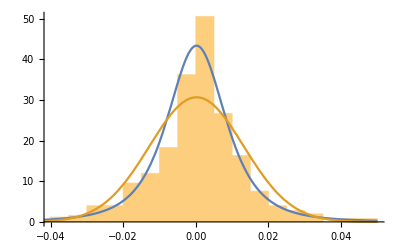

```mathematica
Show[Histogram[return,Automatic,"ProbabilityDensity"],Plot[{PDF[TsallisQGaussianDistribution[0.0002,0.0073, 1.5087],x],PDF[NormalDistribution[0.0002,0.013],x]},{x,-0.05,0.05}]]
```

```mathematica
Drift[μ_,σ_]:=μ+σ^2/2
```

```mathematica
Drift[0.0002, 0.013]
```

0.0002845

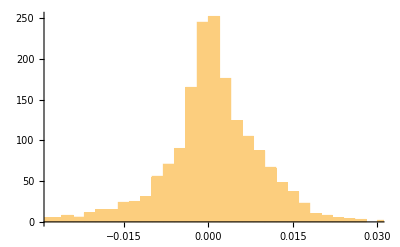

```mathematica
Histogram[return]
```

```mathematica
p =Transpose[Import["C:\\Users\\Eakka\\Documents\\GitHub\\Trading-in-qGaussian\\SatT.csv"]];
p =p[[2]];
p = Delete[p, 1];
```

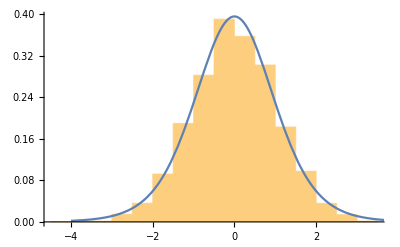

```mathematica
Show[Histogram[p,Automatic,"ProbabilityDensity"],Plot[{PDF[TsallisQGaussianDistribution[0.00039,0.931032512,1.2],x]},{x,-4,4}]]
```

```mathematica
√(1/(2*0.57682))
```

0.931033

```mathematica
Variance[TsallisQGaussianDistribution[μ,β,q]]
```

Piecewise[{{(2 β^2)/(5-3 q), q<5/3}, {∞, 5/3≤q<2}, {Indeterminate, True}}]